```mathematica
SetDirectory[NotebookDirectory[]];
```

Nf=2+1, fixed point expansion, chiral limit

```mathematica
fpiTomqdata={{36.88,150.09},{40.2, 181.11},{42.92, 210.9},{45.22,239.75},{47.23,267.95},{49.02,295.53},{50.65,322},{52.14,349.32}};
```

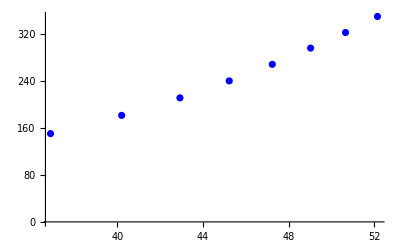

```mathematica
Show[ListPlot[fpiTomqdata,PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
Export["fpiTomq.pdf",ListPlot[fpiTomqdata,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

fpiTomq.pdf

fpi(fixed point p=k)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi1=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf1=ktomf;
```

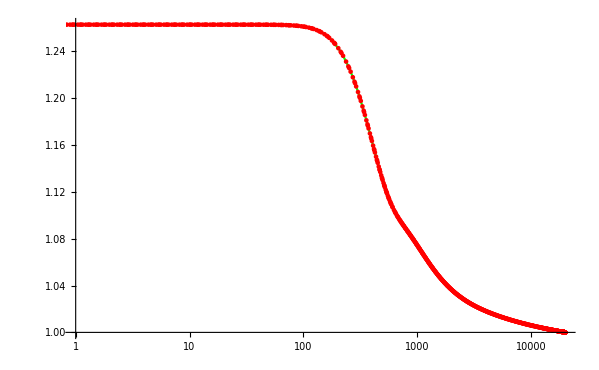

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],ListLogLinearPlot[ktoZpsi,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

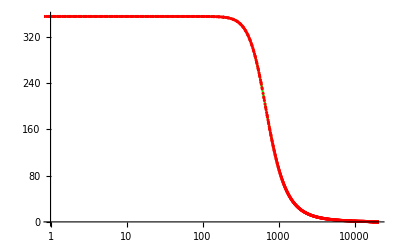

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],ListLogLinearPlot[ktomf,PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf1=ktodmf;
```

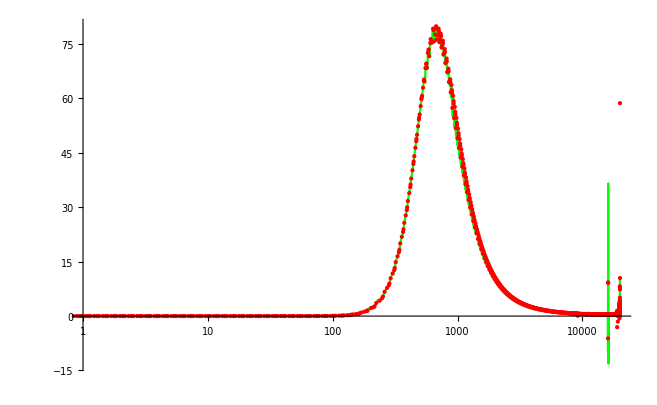

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Green],ListLogLinearPlot[ktodmf,PlotRange->Full ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

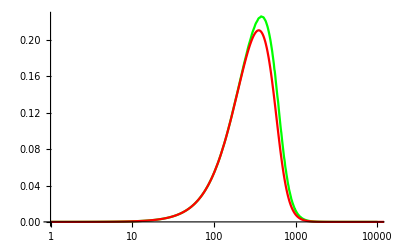

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

7813.89

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

7813.98

```mathematica
√fpi2
```

88.3967

fpi(fixed point p=k,chiral limit,IR=0.068)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi6=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf6=ktomf;
```

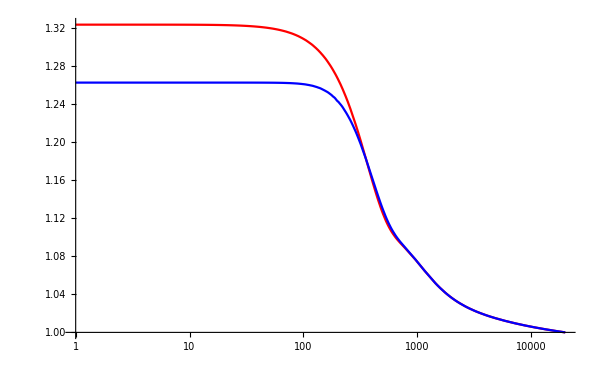

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktoZpsi1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

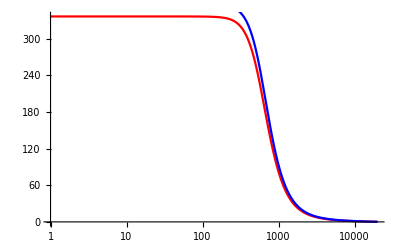

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktomf1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf6=ktodmf;
```

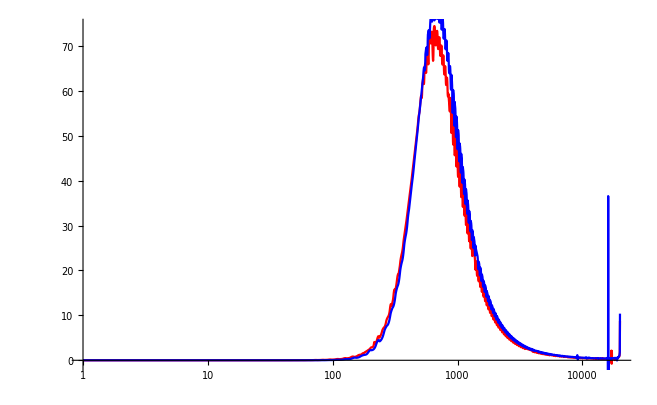

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Red],LogLinearPlot[Interpolation[ktodmf1][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

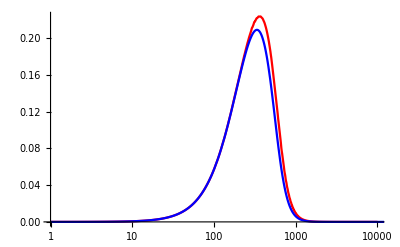

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

7080.98

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

7081.05

```mathematica
√fpi2
```

84.1489

fpi(fixed point p=k,chiral limit,IR=0.06)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d06/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d06/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d06/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi7=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf7=ktomf;
```

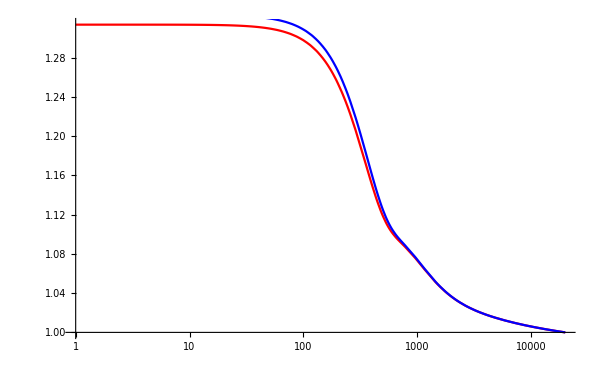

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktoZpsi6][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

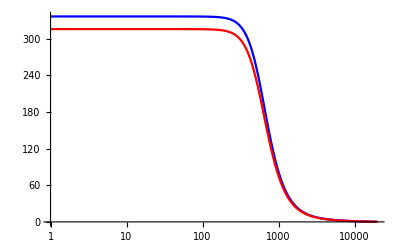

```mathematica
Show[LogLinearPlot[Interpolation[ktomf6][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf7=ktodmf;
```

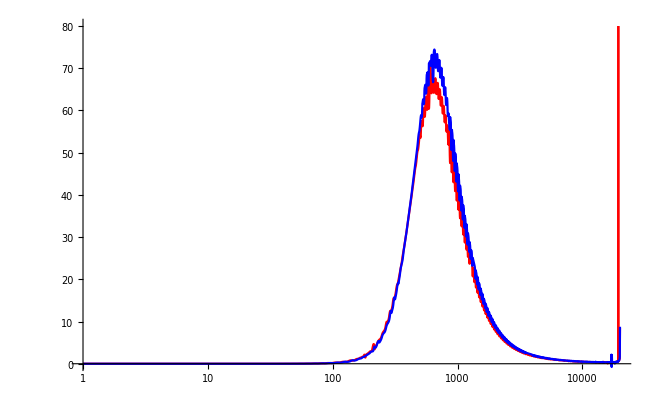

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->{Automatic, {0,80}} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktodmf6][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

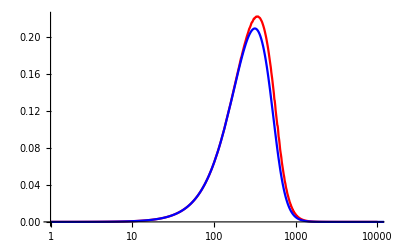

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

6563.84

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

6563.9

```mathematica
√fpi2
```

81.0179

fpi(fixed point p=k,chiral limit,IR=0.063)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d063/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d063/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-IR0d063/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi8=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf8=ktomf;
```

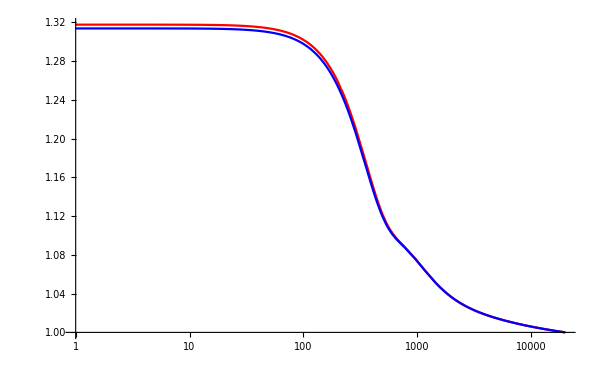

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktoZpsi7][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

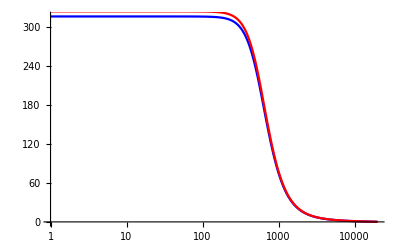

```mathematica
Show[LogLinearPlot[Interpolation[ktomf7][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf8=ktodmf;
```

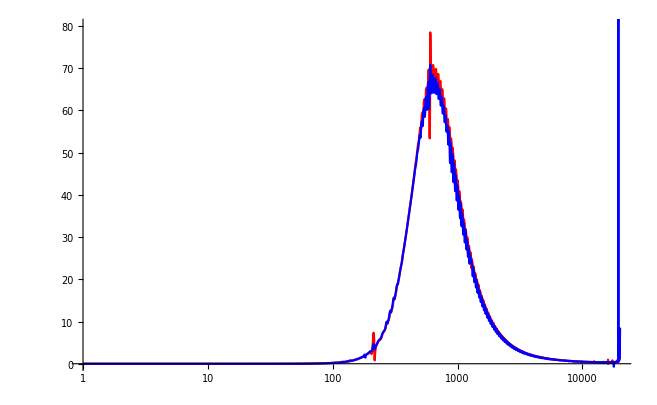

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->{Automatic, {0,80}} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktodmf7][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

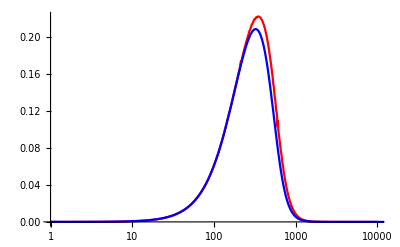

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

6755.13

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

6755.19

```mathematica
√fpi2
```

82.19

fpi(fixed point p=k, scale factor=0.35)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-scale/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-scale/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-scale/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi2=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf2=ktomf;
```

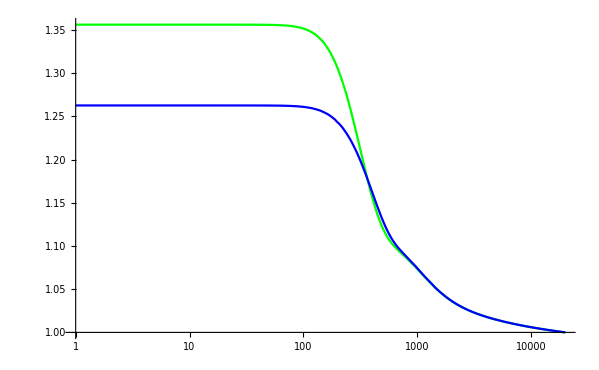

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktoZpsi1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

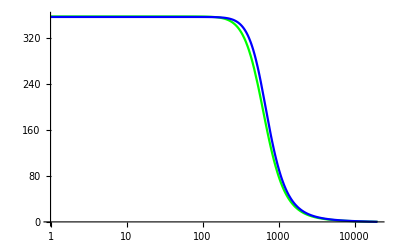

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktomf1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf2=ktodmf;
```

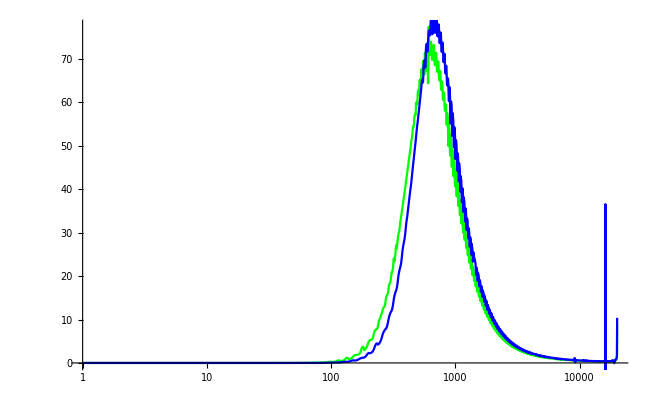

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Green],LogLinearPlot[Interpolation[ktodmf1][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

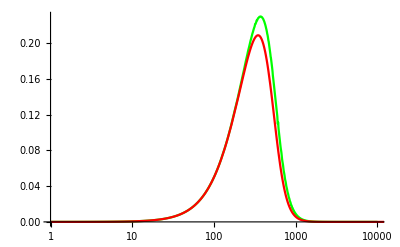

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

6968.09

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

6968.16

```mathematica
√fpi2
```

83.4755

fpi(fixed point p=0)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-p0/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-p0/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-p0/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi3=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf3=ktomf;
```

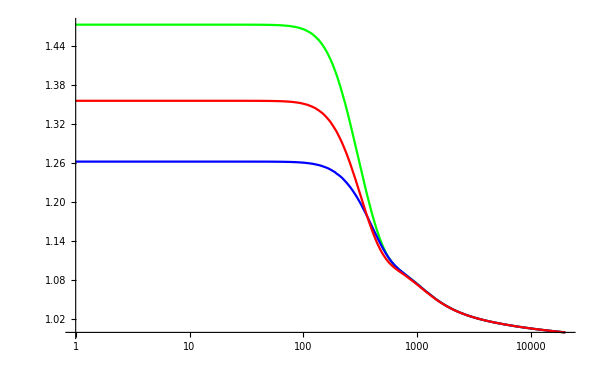

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktoZpsi1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktoZpsi2][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

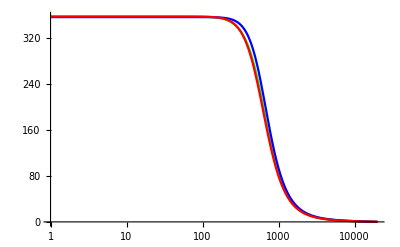

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktomf1][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktomf2][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf3=ktodmf;
```

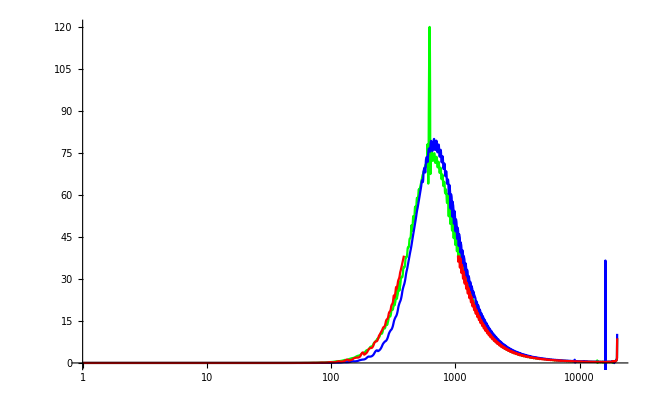

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Green],LogLinearPlot[Interpolation[ktodmf1][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktodmf2][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

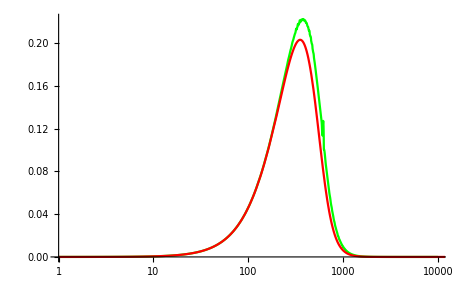

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Green],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

7056.83

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

7056.9

```mathematica
√fpi2
```

84.0053

fpi(fixed point, p=0, IR=0.06)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-IR0d06/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-IR0d06/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-IR0d06/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

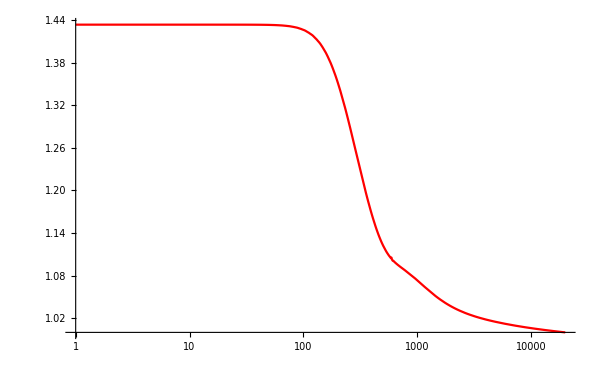

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

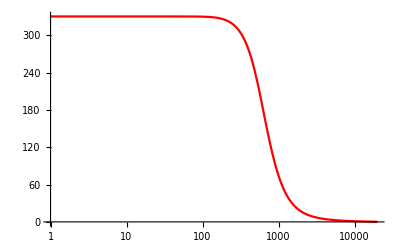

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

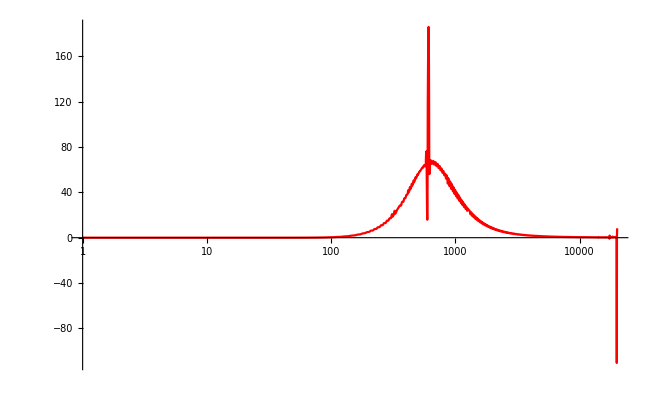

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

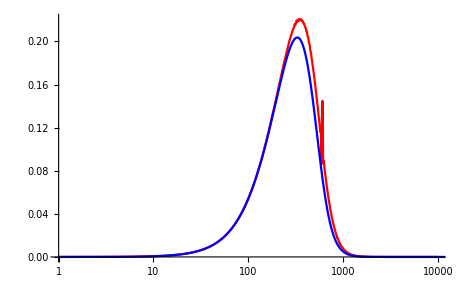

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

6509.39

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

6509.45

```mathematica
√fpi2
```

80.6811

fpi(physical point p=0)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-p0/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-p0/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-p0/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

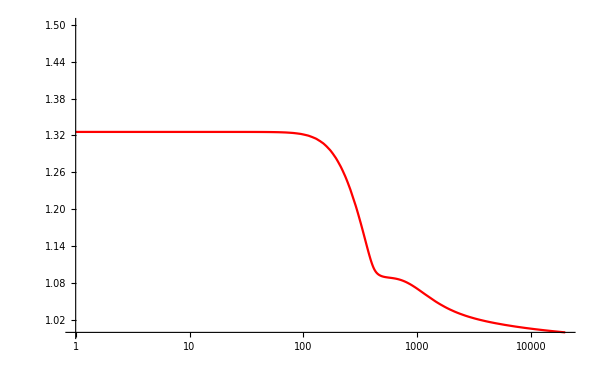

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, {1,1.5}} ,PlotStyle->Red]]
```

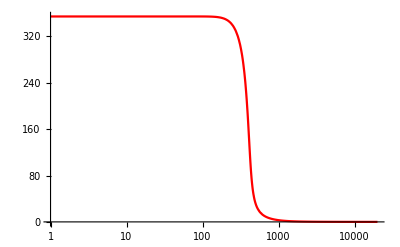

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

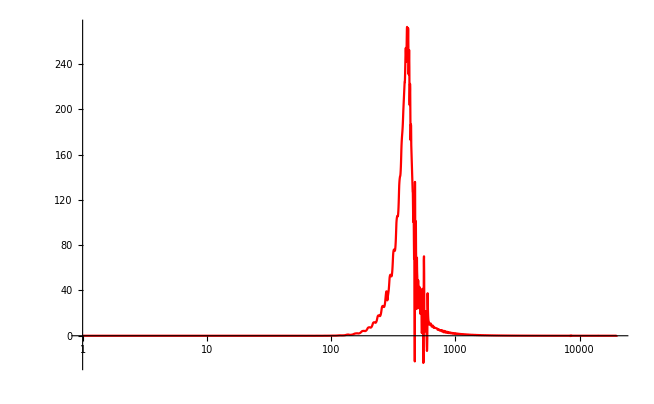

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

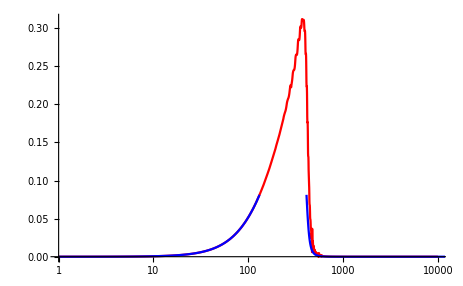

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->Full ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

3170.42

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

3170.42

```mathematica
√fpi2
```

56.3065

```mathematica
56.80650839187961/71.9
```

0.790077

fpi(physical point p=k)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-pk/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-pk/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-IR0d0375-physical-pk/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

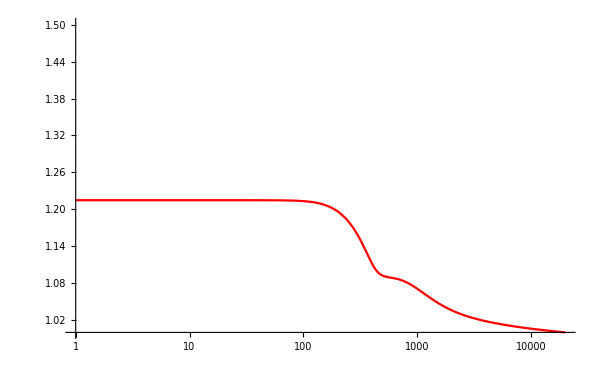

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, {1,1.5}} ,PlotStyle->Red]]
```

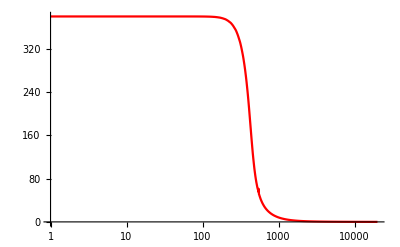

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

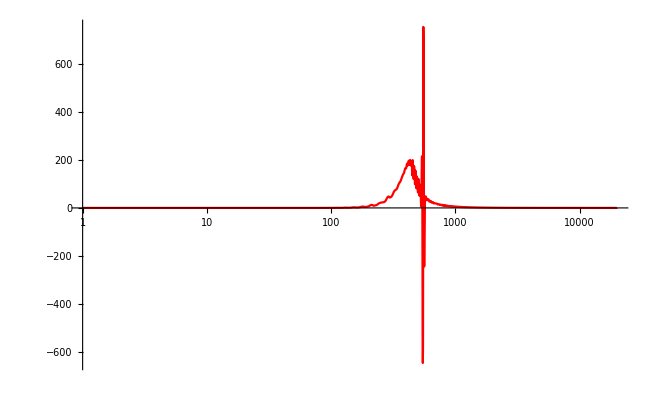

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->Full ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

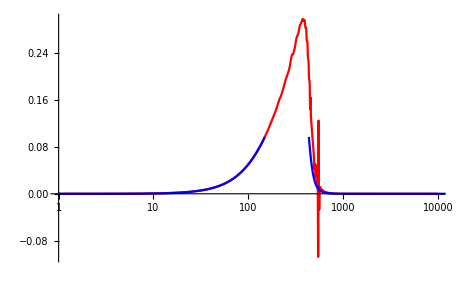

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->Full ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

3777.03

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

3777.03

```mathematica
√fpi2
```

61.4575

```mathematica
56.80650839187961/71.9
```

0.790077

fpi(fixed point p=0, IRstrength=0.0375)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-IR0d0375/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-IR0d0375/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-IR0d0375/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi5=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf5=ktomf;
```

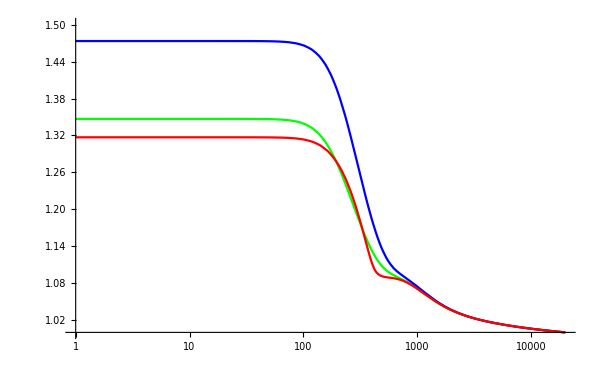

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, {1,1.5}} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktoZpsi3][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktoZpsi4][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

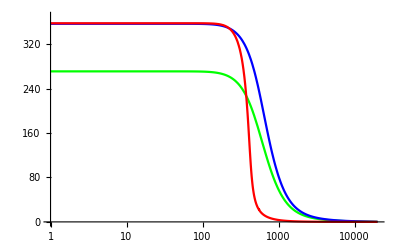

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, {0,370}},PlotStyle->Green],LogLinearPlot[Interpolation[ktomf3][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue],LogLinearPlot[Interpolation[ktomf4][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf5=ktodmf;
```

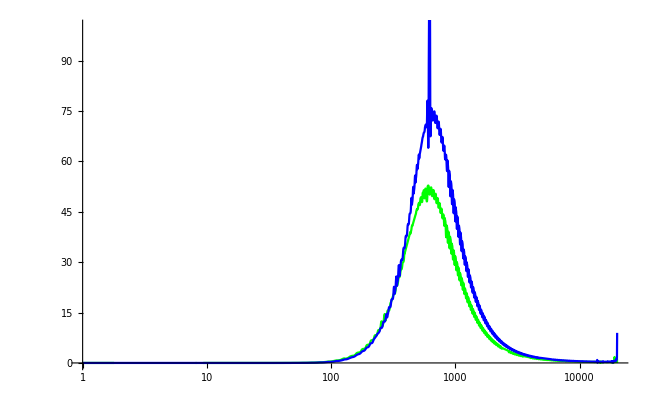

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->{Automatic, {0,100}} ,PlotStyle->Green],LogLinearPlot[Interpolation[ktodmf3][k],{k,1,20000},PlotRange->Full ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

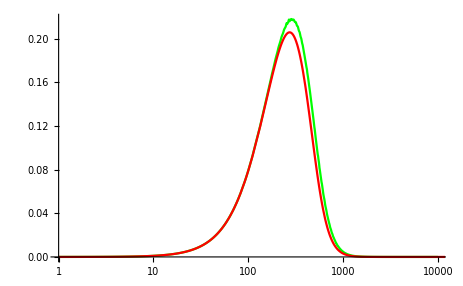

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->Full ,PlotStyle->Green],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

5170.86

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

5170.9

```mathematica
√fpi2
```

71.909

fpi(fixed point p=k,Nf=2,IR=0.03)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-Nf2-IR0d03/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-Nf2-IR0d03/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-Nf2-IR0d03/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi9=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf9=ktomf;
```

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

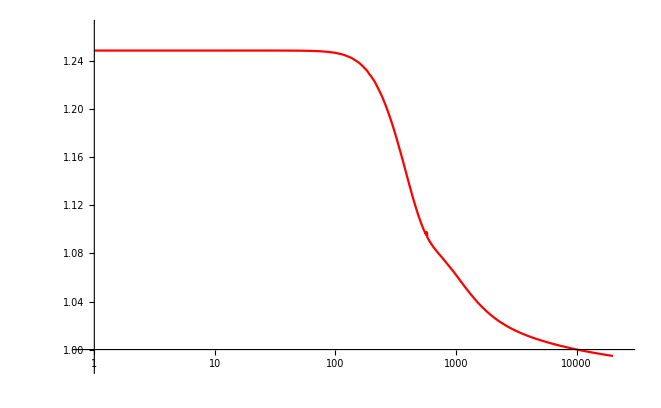

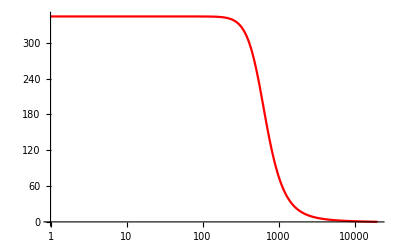

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf9=ktodmf;
```

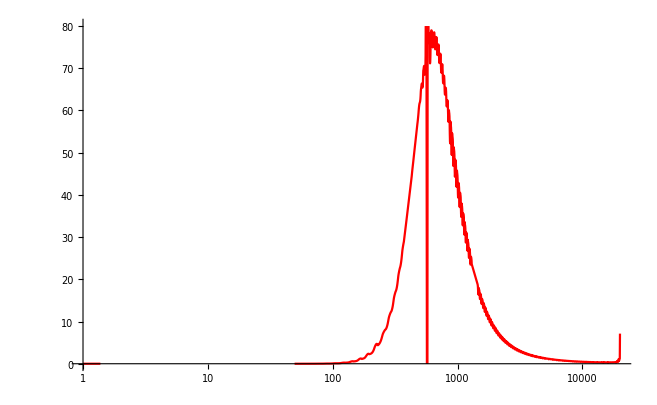

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->{Automatic, {0,80}} ,PlotStyle->Red]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

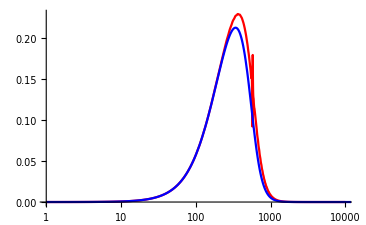

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

7085.05

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

7085.11

```mathematica
√fpi2
```

84.1731

fpi(fixed point p=k, chiral limit, Nf=2,IR=0.03)

```mathematica
kdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-Nf2-IR0d03/kMeV.dat"]];
```

```mathematica
Zpsidata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-Nf2-IR0d03/Zpsi.dat"]];
```

```mathematica
mfdata=  Flatten[Import["./data/T1-muB0-fixed-pk-chiral-limit-Nf2-IR0d03/mf.dat"]];
```

```mathematica
ktoZpsi=Table[{kdata[[i]],Zpsidata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktoZpsi10=ktoZpsi;
```

```mathematica
ktomf=Table[{kdata[[i]],mfdata[[i]]},{i,1,Length[kdata]}];
```

```mathematica
ktomf10=ktomf;
```

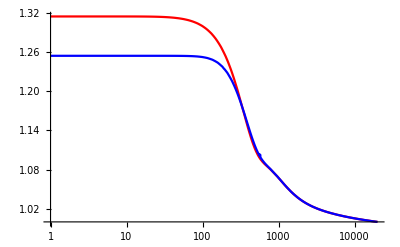

```mathematica
Show[LogLinearPlot[Interpolation[ktoZpsi][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktoZpsi9][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

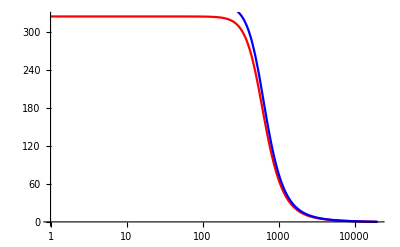

```mathematica
Show[LogLinearPlot[Interpolation[ktomf][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktomf9][k],{k,1,20000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
Zpsifun[k_]:=Interpolation[ktoZpsi][k]
```

```mathematica
mffun[k_]:=Interpolation[ktomf][k]
```

```mathematica
ktodmf=Table[{kdata[[i]],(-y/2 D[ mffun[√y],y]/.{y->kdata[[i]]^2})},{i,1,Length[kdata]}];
```

```mathematica
ktodmf10=ktodmf;
```

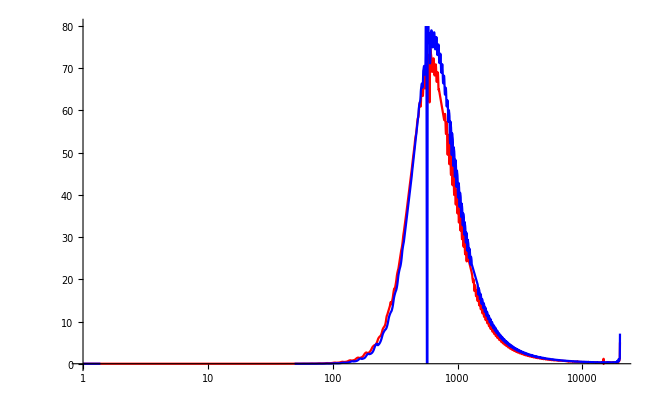

```mathematica
Show[LogLinearPlot[Interpolation[ktodmf][k],{k,1,20000},PlotRange->{Automatic, {0,80}} ,PlotStyle->Red],LogLinearPlot[Interpolation[ktodmf9][k],{k,1,20000},PlotRange->{Automatic, {0,80}} ,PlotStyle->Blue]]
```

```mathematica
dmffun[k_]:=Interpolation[ktodmf][k]
```

```mathematica
kernfun[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y]+dmffun[√y])
```

```mathematica
kernfun2[y_]:=y mffun[√y]/(Zpsifun[√y](y+ mffun[√y]^2)^2)( mffun[√y])
```

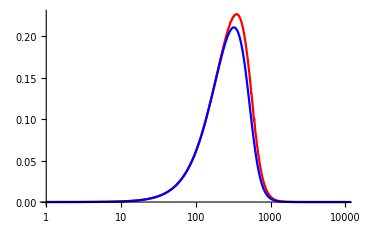

```mathematica
Show[LogLinearPlot[kernfun[k^2],{k,1,10000},PlotRange->{Automatic, Automatic} ,PlotStyle->Red],LogLinearPlot[kernfun2[k^2],{k,1,15000},PlotRange->{Automatic, Automatic} ,PlotStyle->Blue]]
```

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,10000}]
```

6424.7

```mathematica
fpi2=NIntegrate[kernfun[k^2] 3./(4 π^2)2k,{k,1,15000}]
```

6424.74

```mathematica
√fpi2
```

80.1545

```mathematica
84./88
```

0.954545